## Problem 3-15

```mathematica
fccLoc=a{{0,0.5,0.5},{0,0.5,-0.5},{0,-0.5,0.5},{0,-0.5,-0.5},{0.5,0,0.5},{0.5,0,-0.5},{-0.5,0,0.5},{-0.5,0,-0.5},{0.5,0.5,0},{0.5,-0.5,0},{-0.5,0.5,0},{-0.5,-0.5,0}};
Rhat=1/Norm[fccLoc⟦1⟧] fccLoc;
kvec=k{√2,√2,0};
u000={ux,uy,uz};
uother[index_]:={ux ⅇ^(ⅈ Dot[fccLoc⟦index⟧,kvec]),uy ⅇ^(ⅈ Dot[fccLoc⟦index⟧,kvec]),uz ⅇ^(ⅈ Dot[fccLoc⟦index⟧,kvec])};
```

```mathematica
f[index_]:=-α(Dot[Rhat⟦index⟧,u000]-Dot[Rhat⟦index⟧,uother[index]])Rhat⟦index⟧//Simplify;
```

```mathematica
Ftots=f[1]+f[2]+f[3]+f[4]+f[5]+f[6]+f[7]+f[8]+f[9]+f[10]+f[11]+f[12]//Simplify;
FMat=-{{-3+ⅇ^((0.-2.5526554800834367 ⅈ) k)+ⅇ^((0.+2.5526554800834367 ⅈ) k)+0.5 ⅇ^((0.-5.105310960166873 ⅈ) k)+0.5 ⅇ^((0.+5.105310960166873 ⅈ) k), -1+0.5 ⅇ^((0.-5.105310960166873 ⅈ) k)+0.5 ⅇ^((0.+5.105310960166873 ⅈ) k), 0}, {-1+0.5 ⅇ^((0.-5.105310960166873 ⅈ) k)+0.5 ⅇ^((0.+5.105310960166873 ⅈ) k), -3+ ⅇ^((0.-2.5526554800834367 ⅈ) k)+ ⅇ^((0.+2.5526554800834367 ⅈ) k)+0.5 ⅇ^((0.-5.105310960166873 ⅈ) k)+0.5 ⅇ^((0.+5.105310960166873 ⅈ) k), 0}, {0, 0, -4+2 ⅇ^((0.-2.5526554800834367 ⅈ) k)+2 ⅇ^((0.+2.5526554800834367 ⅈ) k)}}; (*I input the values of a=3.61, α=1, and m=1 into FMat*)
```

```mathematica
omegas=Eigensystem[FMat//ExpToTrig]//Simplify
omegas⟦2,2⟧/.k->1 (*Imaginary parts are tiny!*)
```

{{4.-4. Cos[2.55266 k],3.-2. Cos[2.55266 k]+1. √((1.-1. Cos[5.10531 k])^2)-1. Cos[5.10531 k],3.-2. Cos[2.55266 k]-1. √((1.-1. Cos[5.10531 k])^2)-1. Cos[5.10531 k]},{{0,0,1.},{-(1. √((1.-1. Cos[5.10531 k])^2))/(-1.+1. Cos[5.10531 k]),1.,0},{(1. √((1.-1. Cos[5.10531 k])^2))/(-1.+1. Cos[5.10531 k]),1.,0}}}

{1.,1.,0}

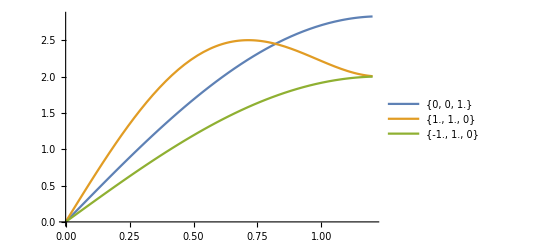

```mathematica
Plot[{√omegas⟦1,1⟧,√omegas⟦1,2⟧,√omegas⟦1,3⟧},{k,0,1.2},PlotLegends->{ToString[omegas⟦2,1⟧],ToString[omegas⟦2,2⟧/.k->1],ToString[omegas⟦2,3⟧/.k->1]}]
```

## Problem 4-1

```mathematica
a=4.04 10^-10;
z=3;
(4z)/a^3
```

1.81986×10^29

## Problem 4-4

```mathematica
A=(.001)^2 π;
i=10;
j=i/A;
e=1.602 10^-19;
z=1;
a=3.61 10^-10;
n=(4z)/a^3;
v=j/(n e)
```

0.000233695

## Problem 4-5

```mathematica
σ=2.38 10^7;
z=1;
a=4.3 10^-10;
n=(2 z)/a^3;
m=9.11 10^-31;
τ=(σ m)/(n e^2)
```

3.3585×10^-14

## Problem 4-7

```mathematica
(*For Sodium*)
z=1;
a=4.3 10^-10;
n=(2 z)/a^3;
R=-1/(n e)
z=1;
a=3.61 10^-10;
n=(4z)/a^3;
R=-1/(n e)
```

-2.48149×10^-10

-7.34174×10^-11

## Problem 4-9

```mathematica
b=1;
ω=(e b)/(2π m)
c=3 10^8;
λ=c/ω
```

2.79875×10^10

0.0107191

## Problem 5-3

```mathematica
Clear[v]
hbar=1.055 10^-34;
λi=1.542 10^-10;
ωi=(2π c)/λi;
ωf=(2 π c)/λf;
ki=(2π)/λi;
kf=(2π)/λf;
Solve[{hbar ωi==hbar ωf+.5 m v^2,hbar ki==-hbar kf+m v},{λf,v}] (*Negative λ makes no sense, so we take the positive one*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{λf→-1.18505×10^-12,v→-6.09294×10^8},{λf→1.59052×10^-10,v→9.2936×10^6}}

## Problem 5-5

```mathematica
Ei=5.6 10^-21;
Ef=10.2 10^-21;
mNeutron = 1.67*^-27;
pf=Sqrt[2 mNeutron Ef]{Sin[45.5π/180],Cos[45.5π/180],0};
pi=Sqrt[2 mNeutron Ei]{-Sin[14π/180],Cos[14 π/180],0};
k=(pf-pi)/hbar;  (*Two orders of magnitude bigger makes the second term negligible *)
Norm[k]
ArcTan[k⟦2⟧/k⟦1⟧]*180/π (* Degrees from the [100] direction *)
```

4.93878×10^10

-1.15793

## Problem 5-6

```mathematica
a=3.61 10^-10;
b1=(4π)/a{-1/2,1/2,1/2};
b2=(4π)/a{1/2,-1/2,1/2};
b3=(4π)/a{1/2,1/2,-1/2};
newk=k-b2-b3;
ArcTan[newk⟦2⟧/newk⟦1⟧]*180/π (* Degrees from the [100] direction *)
Norm[newk]
```

-3.91921

1.4602×10^10

## Problem 5-7

```mathematica
Ef=8 10^-21;
ω=(Ef-Ei)/hbar
pf=Sqrt[2 mNeutron Ef]{Sin[45.5π/180],Cos[45.5π/180],0};
pi=Sqrt[2 mNeutron Ei]{-Sin[14π/180],Cos[14 π/180],0};
k=(pf-pi)/hbar; 
newk=k-b2-b3;
ArcTan[newk⟦2⟧/newk⟦1⟧]*180/π (* Degrees from the [100] direction *)
Norm[newk]
```

2.27488×10^13

-28.3884

1.14285×10^10